```mathematica
Quit[]
```

```mathematica
<<"../orientedGraphTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?contractLorentz 
 ?contractColor 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator
 ----------------------------------------- 
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.
 Make sure you have the "trace_form.log" file for the gamma-algebra

```mathematica
allGraphs=importGraphs["./gammaddBar.qgr"];
```

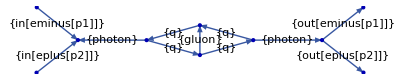

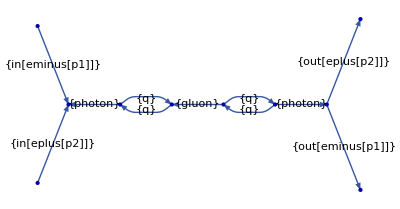

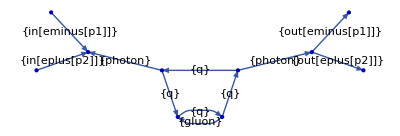

```mathematica
plotGraph[allGraphs,edgeLabels->{"particleType"}]
```

```mathematica
(* isomorphic graphs a summed in the importGraphs function (see numerator for last diagram is actually a sum)*)
allGraphs[[-1,"numerator"]]
```

-in[eminus[p1,-1]] in[eplus[p2,-3]] out[eminus[p1,-2]] out[eplus[p2,-4]] prop[gluon[k1+k2-p1-p2,{11,12}]] prop[photon[-p1-p2,{1,2}]] prop[photon[p1+p2,{3,4}]] prop[q[-k1,{5,6}]] prop[q[k2,{13,14}]] prop[q[-k1+p1+p2,{7,8}]] prop[q[-k1+p1+p2,{9,10}]] v[eplus[-p1,-2],photon[p1+p2,3],eminus[-p2,-4]] v[eplus[p2,-3],photon[-p1-p2,1],eminus[p1,-1]] v[qbar[k1,6],photon[-p1-p2,4],q[-k1+p1+p2,9]] v[qbar[-k2,14],gluon[k1+k2-p1-p2,11],q[-k1+p1+p2,7]] v[qbar[k1-p1-p2,8],photon[p1+p2,2],q[-k1,5]] v[qbar[k1-p1-p2,10],gluon[-k1-k2+p1+p2,12],q[k2,13]]-in[eminus[p1,-1]] in[eplus[p2,-3]] out[eminus[p1,-2]] out[eplus[p2,-4]] prop[gluon[k1+k2-p1-p2,{11,12}]] prop[photon[-p1-p2,{1,2}]] prop[photon[p1+p2,{3,4}]] prop[q[k1,{5,6}]] prop[q[-k2,{13,14}]] prop[q[k1-p1-p2,{7,8}]] prop[q[k1-p1-p2,{9,10}]] v[eplus[-p1,-2],photon[p1+p2,3],eminus[-p2,-4]] v[eplus[p2,-3],photon[-p1-p2,1],eminus[p1,-1]] v[qbar[-k1,6],photon[p1+p2,2],q[k1-p1-p2,7]] v[qbar[k2,14],gluon[-k1-k2+p1+p2,12],q[k1-p1-p2,9]] v[qbar[-k1+p1+p2,8],gluon[k1+k2-p1-p2,11],q[-k2,13]] v[qbar[-k1+p1+p2,10],photon[-p1-p2,4],q[k1,5]]

```mathematica
(* if we process the numerator, one diagram is killed since its 0 due to color *)
```

```mathematica
Length@allGraphs
```

3

```mathematica
?processNumerator
```

```mathematica
allGraphs=processNumerator[allGraphs,"./minFeynRulesQEDQCD.m",algebraOptions->{polarizationSum->True,additionalRules->{SP[p1,p1]->0,d->4}}, symCoefficients->True,coeffFormat->"short"];
```

Final check started

Final check passed

Final check started

Final check passed

```mathematica
allGraphs[[1,"symmetrizedExpandedTensorCoeff"]]
```

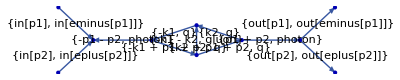

```mathematica
plotGraph[allGraphs[[1]],edgeLabels->{"momentumMap","particleType"},plotSize->Scaled[1]]
```

```mathematica
Length@allGraphs
```

2

```mathematica
allGraphs[[1,-1,-1]]
```

{-(256 ee^4 gs^2 ii^13 TF SP[p1,p2])/(9 (2 SP[p1,p2]+SP[p2,p2])^2)+(256 ee^4 gs^2 ii^13 Nc^2 TF SP[p1,p2])/(9 (2 SP[p1,p2]+SP[p2,p2])^2),{3,3,7,7}}

## Plot graphs (for fresh start: rm -rf a.out *.qgr && gfortran qgraf-3.3.f && ./a.out )

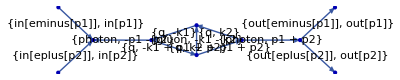

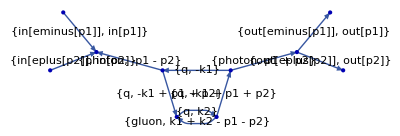

```mathematica
plotGraph[#,edgeLabels->{"particleType","momentumMap"},plotSize->Scaled[0.4]]&/@allGraphs;
```

## Create Cutkovsky-Cuts

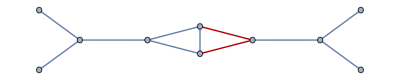

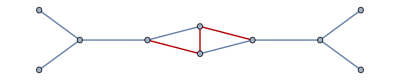

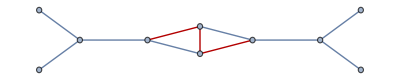

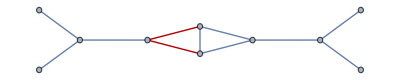

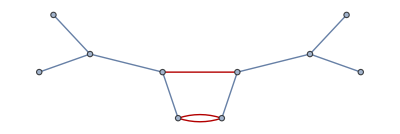

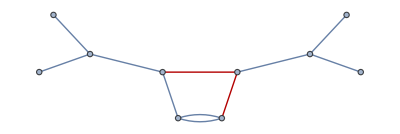

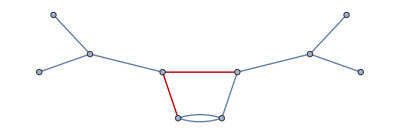

```mathematica
test=constructCuts/@allGraphs;
```

#### see the cut info and selfEnergy info

```mathematica
test[[All,All,"cutInfo"]]//TableForm
```

left
left
right
right
left
right
left
left
cut
cut
left | left
left
right
right
left
right
cut
left
right
cut
cut | left
left
right
right
left
right
left
cut
cut
right
cut | left
left
right
right
left
right
cut
cut
right
right
right
left
left
right
right
left
right
cut
left
right
cut
cut | left
left
right
right
left
right
cut
left
cut
left
left | left
left
right
right
left
right
cut
cut
right
right
right |